```mathematica
SetDirectory["/Users/mirebeau/Dropbox/Programmes/MATLAB/AsymStruct"];
```

```mathematica
DualFinsler[m_,ω_]:=Module[{s=Inverse[m-Transpose[{ω}].{ω}],w}, w=s.ω;{s*(1+w.ω),w}];

VisualizeFinslerMetric[filename_,radius_,subSampling_:1]:=Module[{
metric=Import[filename,"String"],dualMetric,
dims},
(*Import data*)
metric=StringReplace[metric,"e"->"*10^"];
metric=StringSplit[metric];
metric=StringSplit[#,","]&/@metric;
dims=Dimensions@metric;
Assert[Mod[dims[[2]],5]==0];
metric=ArrayReshape[metric,{dims[[1]],dims[[2]]/5,5}];
metric=Transpose@metric;
metric=ToExpression[metric];
dims=Dimensions[metric];
Print["Metric dimension: ",dims,". Components sum: ",Total[metric,3],"."]; (*Check NaN, ...*)

(*subSampling*)
If[subSampling>1,
metric=Table[metric[[i,j,k]],{i,1,dims[[1]],subSampling},{j,1,dims[[2]],subSampling},{k,5}];
dims=Dimensions[metric];
Print["Dimensions after subSampling: ",dims];
];

(*Plotting*)
metric = Map[DualFinsler[{#[[{1,2}]],#[[{2,3}]]},#[[{4,5}]]]&,metric,{2}];
Graphics[
Table[With[{p={i,j},m=radius^2metric[[i,j,1]],ω=radius metric[[i,j,2]]},
{Point[p],Arrowheads[Small],Arrow[{p,p+ ω}], 
GeometricTransformation[{Transparent,EdgeForm[Black],Disk[]},
AffineTransform[{ MatrixPower[m,1/2],p+ ω}]]
}]
,{i,dims[[1]]},{j,dims[[2]]}]
,ImageSize->800]
]
```

Metric dimension: {100,100,5}. Components sum: 1.1268×10^6.

Dimensions after subSampling: {34,34,5}

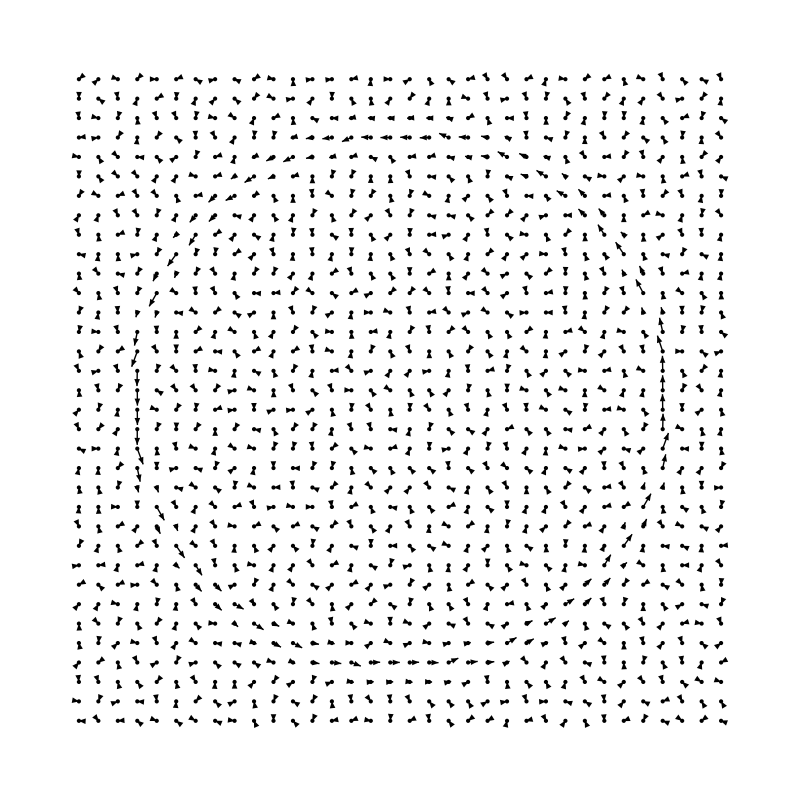

```mathematica
VisualizeFinslerMetric["Output/FinslerNorms.txt",2,3]
```

```mathematica
Export["Output/FinslerMetric.pdf",Out[165]]
```

Output/FinslerMetric.pdf